## functions

```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

## gas

```mathematica
voltageTimestamps=StringSplit[Import[NotebookDirectory[]<>"gas_pulse_times.txt"],"\n"];
```

```mathematica
voltageTimestamps//Column
```

```mathematica
startDate=DateObject[voltageTimestamps[[1]]]
```

Wed 22 Nov 2023 17:11:33GMT+1

```mathematica
startDate=DateObject["2023.11.23. 00:00"]
```

Minute: Thu 23 Nov 2023 00:00GMT+1

```mathematica
timeGranularity="Minute";
```

```mathematica
voltageTimes=Map[
Round[DateDifferenceInUnits[startDate,DateObject[#],timeGranularity]]
&,voltageTimestamps];
```

```mathematica
gasTimes=Map[Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity]]&,Select[Transpose[{Drop[voltageTimestamps,1],Differences[voltageTimes]}],1<#[[2]]&]];
```

```mathematica
gasTimes//N
```

```mathematica
{6.,9.,12.,14.,18.,24.,30.,33.,36.,39.,42.,44.,47.,51.,54.,59.,62.,67.,69.,71.,78.,86.,91.,97.,99.,101.,116.,122.,127.,129.,133.,136.,156.,160.,165.,169.,171.,173.,175.,177.,183.,186.,189.,192.,195.,197.,199.,201.,203.,205.,211.,217.,220.,224.,226.,230.,232.,235.,238.,242.,245.,249.,251.,254.,256.,258.,261.,266.,270.,273.,280.,283.,289.,302.,307.,309.,314.,327.,330.,334.,342.,346.,349.,352.,356.,366.,375.,378.,382.,385.,389.,392.,396.,399.,402.,405.,409.,412.,416.,427.,431.,435.,441.,444.,447.,450.,454.,457.,461.,464.,467.,471.,474.,478.,481.,485.,515.,543.,547.,549.,552.,555.,558.,561.,564.,568.,571.,574.,578.,581.,588.,591.,594.,597.,603.,610.,612.,617.,619.,622.,628.,631.,638.,643.,646.,651.,655.,661.,664.,667.,675.,678.,682.,686.,688.,694.,697.,703.,706.,713.,719.,721.,728.,739.,743.,746.,752.,756.,762.,765.,768.,791.,798.,800.,803.,807.,810.,813.,816.,828.,832.,840.,855.,857.,859.,863.,865.,867.,869.,871.,873.,875.,878.,881.,884.,886.,888.,890.,892.,894.,896.,898.,900.,902.,904.,908.,910.,913.,915.,917.,919.,921.,923.,925.,927.,929.,931.,936.,938.,940.,942.,944.,947.,950.,955.,959.,961.,964.,966.,969.,974.,986.,1000.,1008.,1012.,1019.,1023.,1026.,1029.,1031.,1034.,1036.,1038.,1040.,1042.,1044.,1046.,1048.,1053.,1058.,1065.,1077.,1080.,1082.,1094.,1104.,1106.,1108.,1111.,1114.,1116.,1121.,1126.,1129.,1132.,1135.,1140.,1155.,1158.,1160.,1163.,1166.,1169.,1177.,1186.,1189.,1193.,1195.,1210.,1213.,1217.,1220.,1223.,1229.,1231.,1233.,1236.}
```

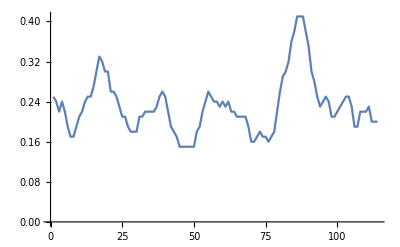

```mathematica
ListPlot[MovingAverage[BinCounts[gasTimes,{0,Max[gasTimes],10}]0.1,10],Joined->True]
```

## heat

```mathematica
groundTruth={
{3786,5334},
{1585,8044},
{222,6678},
{44,1044}
};(*fűtési, hűtési*)
```

```mathematica
FormatHeatmeterEntry[entry_]:=Module[
{list},
list=StringSplit[entry,""]/.{"-"->-1};
Table[
If[list[[pos]]==-1,
Nothing,
If[
1<pos&&list[[pos-1]]==-1,
-ToExpression[list[[pos]]],
ToExpression[list[[pos]]]
]]
,{pos,1,Length[list]}]
]
```

```mathematica
startDate=DateObject["2023.11.21. 21:45"];
```

```mathematica
timeGranularity="Minute";
```

```mathematica
readout=Map[
Join[
{Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity],0.25]},
Map[
FormatHeatmeterEntry[#]
&,#[[2;;5]]]
]
&,Map[
StringSplit[#,","]
&,StringSplit[Import[NotebookDirectory[]<>"heatmeter_readouts.csv","Text"],"\n"]]];
```

```mathematica
heatingCumulativeUnclean=Table[DeleteDuplicates[Select[Map[
{#[[1]],ToExpression[StringRiffle[#[[2]],""]]}&,
Select[
Transpose[Transpose[readout][[{1,cycle+1}]]],
MemberQ[#[[2]],-1]==False&
]],#[[2]]-groundTruth[[cycle]][[1]]<1500&]],{cycle,1,4}];
```

```mathematica
heatingCumulativeClean=Table[Table[
If[
10<Abs[heatingCumulativeUnclean[[cycle]][[n]][[2]]-heatingCumulativeUnclean[[cycle]][[n-1]][[2]]],
Nothing,
heatingCumulativeUnclean[[cycle]][[n]]
]
,{n,2,Length[heatingCumulativeUnclean[[cycle]]]}],{cycle,1,4}];
```

```mathematica
heatingDiff=Table[Table[
{Mean[{heatingCumulativeClean[[cycle]][[n]][[1]],heatingCumulativeClean[[cycle]][[n-1]][[1]]}],(heatingCumulativeClean[[cycle]][[n]][[2]]-heatingCumulativeClean[[cycle]][[n-1]][[2]])/(heatingCumulativeClean[[cycle]][[n]][[1]]-heatingCumulativeClean[[cycle]][[n-1]][[1]])}
,{n,2,Length[heatingCumulativeClean[[cycle]]]}],{cycle,1,4}];
```

Power::infy: Infinite expression 1/0. encountered.

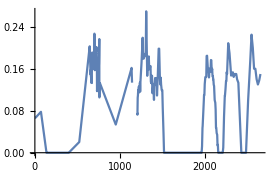
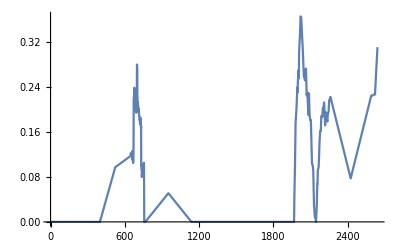
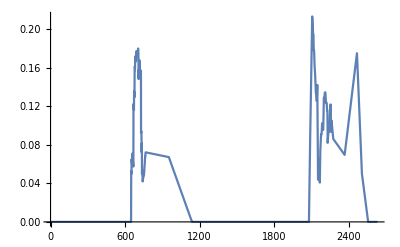
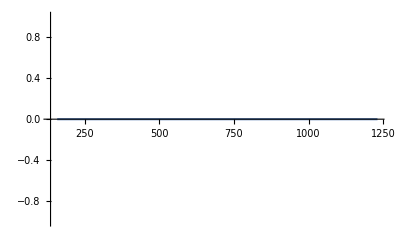

```mathematica
Table[
ListPlot[SparseTimeMovingAverage[heatingDiff[[cycle]],60 1],Joined->True,PlotRange->All]
,{cycle,1,4}]
```

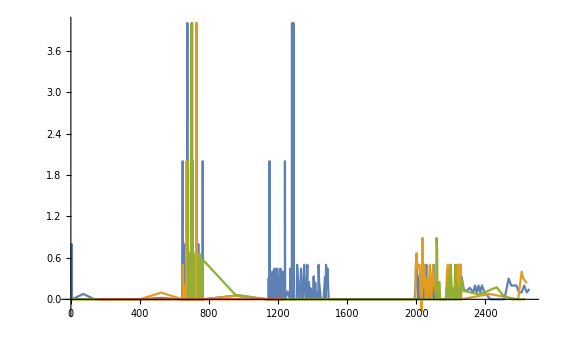

```mathematica
ListPlot[heatingDiff,Joined->True,PlotRange->All]
```